```mathematica
ClearAll["Global`*"]
```

## Full Expressions for Regret

```mathematica
R = a(T-T/K) - (a+1/2)T/2Sqrt[-Log[1-4a^2](T/K + N)] + N/2 (*The exact expression for regret *)
R00 = a(T) - (a+1/2)T/2Sqrt[4a^2(T/K + N)] + N/2 (* Simplified by dropping the -T/K term and approximating the log expression with 4a^2 *)
R2 = a(T) - (a+1/2)T/2Sqrt[8a^2N] + N/2 (*As above but assuming N > T/K*)
R3 = a (T - T/2Sqrt[T/K+N])+N/2 (*Drops -T/K term, approximates log, assumes a << 1/2*)
R4 =  1/2(T - T/2Sqrt[N])+N/2  (*As above with a =1/2 (highest regret) and dropping T/K term inside sqrt (also should increase regret bound)*)
```

N/2+a (T-T/K)-1/2 (1/2+a) T √(-(N+T/K) Log[1-4 a^2])

N/2+a T-(1/2+a) T √(a^2 (N+T/K))

N/2+a T-√2 (1/2+a) √(a^2 N) T

N/2+a (T-1/2 T √(N+T/K))

N/2+1/2 (T-(√N T)/2)

### Messing around

```mathematica
Expand[(a+b)(a-b)]
```

a^2-b^2

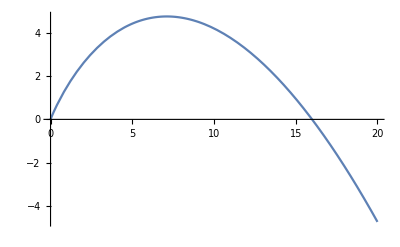

```mathematica
Plot[2T - T^(3/2)/2,{T,0,20}]
```

```mathematica
Solve[2T - T^(3/2)/2 ==0,T]
```

{{T→0},{T→16}}

```mathematica
Solve[D
```

```mathematica
Series[-Log[1-4a^2],{a,0,4}]
```

4 a^2+8 a^4+O[a]^5

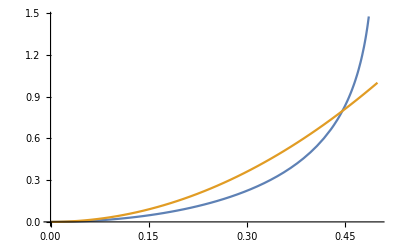

```mathematica
Plot[{-1/2Log[1-4a^2],4a^2},{a,0,.5}]
```

```mathematica
Rtk = R//.{T->1000,K->500}
```

998 a+N/2-500 (1/2+a) √(-(2+N) Log[1-4 a^2])

```mathematica
avals = Range[0,.006,.001]
```

{0.,0.001,0.002,0.003,0.004,0.005,0.006}

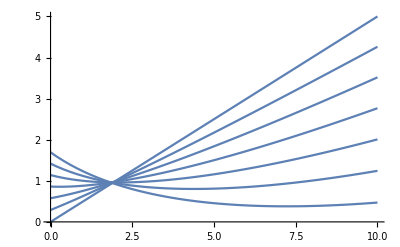

```mathematica
Plot[Rtk /. a -> avals,{N,0,10}]
```

```mathematica
R3
```

N/2+a (T-1/2 T √(N+T/K))

```mathematica
Solve[D[R3,a]==0,a]
```

{{}}

a T+1/2 (-T/K+(a^2 T^2)/4)-√2 (1/2+a) T √(a^2 (-T/K+(a^2 T^2)/4))

a (T-T/K)+1/2 (-T/K+(a^2 T^2)/4)-1/4 (1/2+a) T √(-a^2 T^2 Log[1-4 a^2])

{T→1000,K→500}

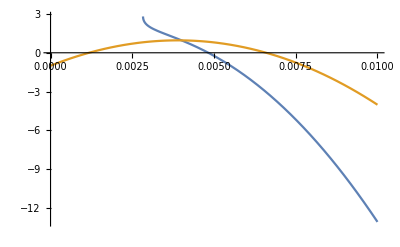

```mathematica
R3 = R2/.N->-T/K+(a^2 T^2)/4
R4 = R /. N->-T/K+(a^2 T^2)/4
v = {T->1000,K->500}
Plot[{R3//.v, R4 //.v},{a,0,.01}]
```

```mathematica
amin = Solve[D[R3,a]==0,a]
```

{{a→(-T-√T √(192+T))/(12 T)},{a→(-T+√T √(192+T))/(12 T)},{a→(-3 T-√3 √(-64 T+3 T^2))/(12 T)},{a→(-3 T+√3 √(-64 T+3 T^2))/(12 T)}}

```mathematica
N[Values[amin]/.T->1000]
```

{{-0.174316},{0.00764896},{-0.497319},{-0.00268104}}

a→1/12 (-1+√((192+T)/T))

990 a+62500 a^2-500 (1/2+a) √(-(10+125000 a^2) Log[1-4 a^2])

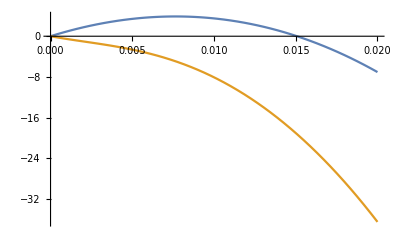

```mathematica
Simplify[a->(-T+√T √(192+T))/(12 T),T>0]
```

### T < K^3/16

```mathematica
R4 = Expand[R3 /.{a->(8T)^(-1/3),N->T,K->2(16T)^(1/3)}]
```

T^(2/3)/2+T/2-1/4 T^(2/3) √(T^(2/3)/(4 2^(1/3))+T)

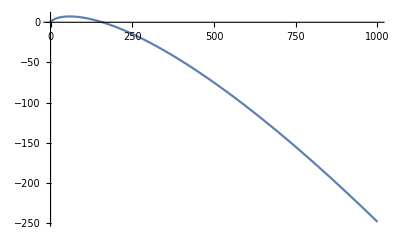

```mathematica
Plot[R4,{T,0,1000}]
```

```mathematica
R4 = N/2+T^(2/3)/2^(1/3)-((1/2) T √((N+T/K)/T^(2/3)))/2^(1/3)
```

N/2+T^(2/3)/2^(1/3)-(T √((N+T/K)/T^(2/3)))/(2 2^(1/3))

```mathematica
R5 = N - T^(2/3)Sqrt[N+T/K]
Expand[Solve[D[R5,N]==0,N]]
```

N-T^(2/3) √(N+T/K)

{{N→-T/K+T^(4/3)/4}}

```mathematica
N->-T/K+T^(4/3)/4//.{T->1000,K-> 125}
```

N→2492

```mathematica
N[5*(16*1000)^(1/3)]
```

125.992

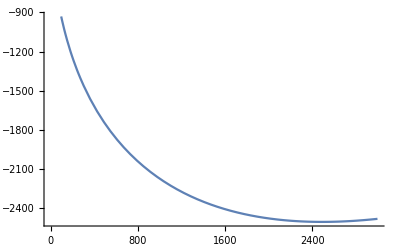

```mathematica
Plot[N-T^(2/3) √(N+T/K)//.{T->1000,K-> 125},{N,0,3000}]
```

```mathematica
amax = {a->(2T)^-(1/3)}
R3 = R00/.amax
Nmin = {N->T}(*Expand[Solve[D[R3,N]==0,N]]*)
Regret = ExpandAll[Simplify[R3 /.Nmin,{T>0,K>0}]]
```

{a→1/(2^(1/3) T^(1/3))}

N/2+T^(2/3)/2^(1/3)-((1/2+1/(2^(1/3) T^(1/3))) T √((N+T/K)/T^(2/3)))/2^(1/3)

{N→T}

T^(2/3)/2^(1/3)-(√(1+1/K) T^(5/6))/2^(2/3)+T/2-(√(1+1/K) T^(7/6))/(2 2^(1/3))

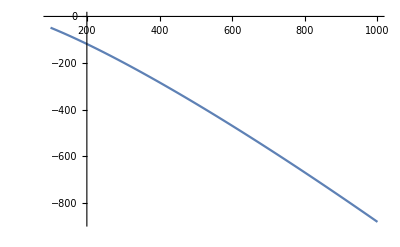

```mathematica
Plot[Regret //.K->100,{T,100,1000}]
```

```mathematica
Simplify[(17 T^(2/3))/(16 2^(1/3))-(√(2^(1/3) T^(2/3)) T^(2/3))/(16 2^(1/6))+T/16-T/(2 K)-(√(2^(1/3) T^(2/3)) T)/(16 2^(5/6))+T^(4/3)/(32 2^(2/3))]
```

```mathematica
Simplify[(√(2^(1/3) T^(2/3)) T^(2/3))/(16 2^(1/6))]
```

T/16

```mathematica
Simplify[(√(2^(1/3) T^(2/3)) T)/(16 2^(5/6))]
```

T^(4/3)/(16 2^(2/3))

### T > K^3/16

{a→(√(K/T))/2}

N/2+1/2 √(K/T) T-1/4 (1/2+(√(K/T))/2) T √((K (N+T/K))/T)

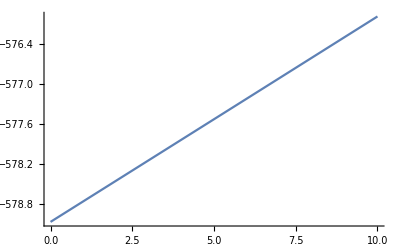

{N→0}

1/8 (-1+3 √(K/T)) T

```mathematica
amax = {a->1/2Sqrt[K/T]}
R3 = R00/.amax
Plot[R3//.{T->5000,K->3},{N,0,10}]
Nmin = {N->0} (* Need to justify why this is correct *)
Regret = Simplify[R3 /.Nmin,{T>0,K>0}]
```

```mathematica
N[Nmin //.{T->5000,K->5}]
```

{{N→-584.279}}

## Regret for time varying graph, assuming N0 < aT

```mathematica
ClearAll["Global`*"]
```

```mathematica
R = a(T - T/K - T a Sqrt[2 T(1/K+a/m)])
R0 =  a(T - T a Sqrt[2 T(1/K+a/m)])
R1 = a (T-√2 a T √((1/K) T))
R2 = a (T-√2 a T √(a T/m))
R3 =a(T - T a (Sqrt[2 T(1/K)]+Sqrt[2 T(a)]))
```

a (T-T/K-√2 a T √((1/K+a/m) T))

a (T-√2 a T √((1/K+a/m) T))

a (T-√2 a T √(T/K))

a (T-√2 a T √((a T)/m))

a (T-a T (√2 √(a T)+√2 √(T/K)))

```mathematica
Solve[D[R2,a]==0,a]
```

{{a→-((-2)^(1/3) m^(1/3))/(5^(2/3) T^(1/3))},{a→(2^(1/3) m^(1/3))/(5^(2/3) T^(1/3))},{a→((-1)^(2/3) 2^(1/3) m^(1/3))/(5^(2/3) T^(1/3))}}

```mathematica
Maximize[R1,a]
```

{Piecewise[{{(√(K T))/(4 √2), T>0&&K>0}, {-∞, !((T==0&&K>0)||(T==0&&K<0)||(T>0&&K>0)||(T<0&&K<0))}, {∞, T<0&&K<0}, {0, True}}],{a→Piecewise[{{Indeterminate, !((T==0&&K>0)||(T==0&&K<0)||(T>0&&K>0))}, {Root[-K^2+8 √2 K √(K T) #1-32 K T #1^2+64 T^2 #1^4&,3], T>0&&K>0}, {0, True}}]}}

### Large K - (1/K << a/m)

```mathematica
R4 = Expand[Simplify[ R /. a->(16T)^(-1/3)m^(1/3)]]
```

(m^(1/3) T^(2/3))/(2 2^(1/3))-(m^(1/3) T^(2/3))/(2 2^(1/3) K)-(m^(2/3) T^(1/3) √((2^(2/3) T^(2/3))/m^(2/3)+(4 T)/K))/(8 2^(1/6))

```mathematica
Reduce[(2^(2/3) T^(2/3))/m^(2/3)>(4 T)/K,T,Reals]
```

m>0&&((K<0&&T>0)||(K>0&&0<T<K^3/(16 m^2)))

```mathematica
R5 = (m^(1/3) T^(2/3))/(2 2^(1/3))-(m^(1/3) T^(2/3))/(2 2^(1/3) K)-Simplify[(m^(2/3) T^(1/3) √(2(2^(2/3) T^(2/3))/m^(2/3)))/(8 2^(1/6)),T>0]
```

(m^(1/3) T^(2/3))/(4 2^(1/3))-(m^(1/3) T^(2/3))/(2 2^(1/3) K)

### Small K - (1/K > a/m)

## Expressions for Regrest assuming N0 < aT

```mathematica
R = a(T  - T/K-  Sqrt[2 a^2T^3(1/K + a )] )+  N/2
```

N/2+a (T-T/K-√2 √(a^2 (a+1/K) T^3))

```mathematica
R1 =  a(T  - a T Sqrt[2T(1/K + a )] )+  N/2
```

N/2+a (T-√2 a T √((a+1/K) T))

```mathematica
R2 =Expand[Simplify[R /. {N->0,a -> (16T)^(-1/3)},T > 0]]
```

T^(2/3)/(2 2^(1/3))-T^(2/3)/(2 2^(1/3) K)-(√(2^(2/3)+(4 T^(1/3))/K) T^(2/3))/(8 2^(1/6))

```mathematica
Simplify[1/(2 2^(1/3))-1/(2 2^(1/3) K)-(√(2*2^(2/3)))/(8 2^(1/6))]
```

```mathematica
Simplify[(√(2*2^(2/3)))/(8 2^(1/6))]
```

```mathematica
Simplify[1/(4 2^(1/3))*2 2^(1/3)]
```

```mathematica
Simplify[1/(8 2^(1/6))*2 2^(1/3)]
```

1/(2 2^(5/6))

```mathematica
Simplify[(√(2*2^(2/3)))/(2 2^(5/6))]
```

1/2

```mathematica
Simplify[√(2*2^(2/3))]
```

2^(5/6)

```mathematica
1/2-1/3
```

```mathematica
3*6*(16)^(1/3)
```

```mathematica
N[36 2^(1/3)]
```

45.3572

```mathematica
Reduce[2^(2/3)>(4 T^(1/3))/K,T]
```

(K<0&&T≥0)||(K==0&&T==0)||(K>0&&0≤T<K^3/16)

```mathematica
(8 2^(1/6))/(2 2^(1/3))
```

2 2^(5/6)

```mathematica
1+5/6
```

```mathematica
1+2/3
```

5/3

```mathematica
5/3*1/2
```

5/6

```mathematica
5/6+6/11
```

91/66

```mathematica
N[2^(6/11)]
```

1.45948

```mathematica
N[2^(6/12)]
```

1.41421

```mathematica
N[Sqrt[2]]
```

1.41421

```mathematica
(16)^{1/3}
```

{2 2^(1/3)}

```mathematica
2^3
```

```mathematica
1/6 + 3
```

19/6

```mathematica
1+1/3
```

4/3

```mathematica
N[2^(4/3)]
```

5.33333

```mathematica
N[16^(1/3)]
```

2.51984

```mathematica
Solve[(b Sqrt[K/T] /. {K->(16T)^(1/3)} )== (16T)^(-1/3),b]
```

{{b→1/4}}

### if K < (16T)^1/3

```mathematica
R2 =Expand[ R /. {N->0,a -> 1/4Sqrt[K/T]}]
```

1/4 √(K/T) T-(√(K/T) T)/(4 K)-(√(K/T) √(K (1/K+(√(K/T))/4) T^2))/(8 √2)

```mathematica
p1 = Simplify[Part[R2,1],{K>0,T>0}]
```

(√(K T))/4

```mathematica
p2 = Simplify[Part[R2,2],{K>0,T>0}]
```

-T/(4 √(K T))

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0 == -√K\ √T - √K\ T, 0 == -K\ √Power[« 2 »]\ T + √K\ T/K, 0 == √K\ √T - √K\ T, 0 == -K\ √Power[« 2 »]\ T + √K\ T/K}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(0==-√K √T-√(K T)&&K≠0&&0==(-K √(T/K)+√(K T))/K&&√(K T)≠0)||(0==√K √T-√(K T)&&K≠0&&0==(-K √(T/K)+√(K T))/K&&√(K T)≠0)

```mathematica
p3 = Simplify[Part[R2,3],{K>0,T>0}]
```

-(√(K (4+√(K^3/T)) T))/(16 √2)

```mathematica
Expand[K (4+√(K^3/T)) T]
```

4 K T+K √(K^3/T) T

```mathematica
Sqrt[8]
```

2 √2

```mathematica
1/4 - 1/8
```

1/8

```mathematica
R6 = 1/8Sqrt[K T] - 1/4 Sqrt[T/K]
```

-(√(T/K))/4+(√(K T))/8

```mathematica
R6 /. K-> 3
```

-(√T)/(4 √3)+(√3 √T)/8

```mathematica
Reduce[c √3 √T > -(√T)/(4 √3)+(√3 √T)/8,c]
```

T>0&&c>1/24

```mathematica
24*3
```

72

```mathematica
Reduce[1/8Sqrt[K T] > 1/4 Sqrt[T/K],T]
```

(K<-2&&T<0)||(K>2&&T>0)

```mathematica
Reduce[4 K T  > K √(K^3/T) T,T]
```

(K<0&&T<K^3/16)||(K>0&&T>K^3/16)

```mathematica
Simplify[√(K ^2 T^(2/4)(√K+2^(2/3) T^(1/6))) ]
```

```mathematica
Expand[K ^2 T^(2/4)(√K+2^(2/3) T^(1/6))]
```

K^(5/2) √T+2^(2/3) K^2 T^(2/3)

```mathematica
Reduce[K^(5/2) √T <2^(2/3) K^2 T^(2/3),T]
```

K>0&&T>K^3/16

```mathematica
R3 = p1 + p2-Simplify[(√(2*2^(2/3) K^2 T^(2/3)))/(16 √2),{T > 0,K > 0}]
```

-(√K T^(1/6))/(8 2^(1/3))-(K T^(1/3))/(8 2^(2/3))+(√(K T))/4

```mathematica
Reduce[1/2(√(K T))/4 > (K T^(1/3))/(8 2^(2/3)),T]
Reduce[1/2(√(K T))/4 >(√K T^(1/6))/(8 2^(1/3)),T]
```

K>0&&T>K^3/16

K>0&&T>1/2

```mathematica
1/4Sqrt[K/T]/. K-> (16T)^(1/3)
```

1/(2 2^(1/3) T^(1/3))

```mathematica
16^(1/3)
```

2 2^(1/3)

```mathematica
Simplify[(K √(√K) T^(1/4))/(16 √2),{K>0,T>0}]+Simplify[(K √(2^(2/3) T^(1/6)) T^(1/4))/(16 √2),{K>0,T>0}]
```

(K T^(1/3))/(16 2^(1/6))+((K^5 T)^(1/4))/(16 √2)

```mathematica
N[Reduce[(√(K T))/4>(√K T^(1/6))/(8 2^(1/3)),T]]
N[Reduce[(√(K T))/4>(K √(√K+2^(2/3) T^(1/6)) T^(1/4))/(16 √2),T]]
```

K>0.&&T>0.0625

K>0.&&T>Root[-K^9+2320 K^6 #1-3407872 K^3 #1^2+1073741824 #1^3&,1]

```mathematica
N[1/16]
```

0.0625

```mathematica
Simplify@Level[R2,{1}]
```

{-(√(K/T) T^(2/3))/(8 2^(1/3)),1/4 √(K/T) T,-(√(K/T) √(2^(2/3) K T^(5/3)+(K/T)^(3/2) T^3))/(16 √2)}

```mathematica
List[Expand[R2]]
```

{-(√(K/T) T^(2/3))/(8 2^(1/3))+1/4 √(K/T) T-(√(K/T) √(K ((√(K/T))/4+1/(2 2^(1/3) T^(1/3))) T^2))/(8 √2)}

```mathematica
l =  List[Expand[R2]]
```

{-(√(K/T) T^(2/3))/(8 2^(1/3))+1/4 √(K/T) T-(√(K/T) √(K ((√(K/T))/4+1/(2 2^(1/3) T^(1/3))) T^2))/(8 √2)}

```mathematica
Part[l,1]
```

-(√(K/T) T^(2/3))/(8 2^(1/3))+1/4 √(K/T) T-(√(K/T) √(K ((√(K/T))/4+1/(2 2^(1/3) T^(1/3))) T^2))/(8 √2)

## Expressions for Regret (assuming E_unif[N0] = E*[N0])

```mathematica
R = a(T -T/K - T/2Sqrt[-Log[1-4a^2](T/K + N)] )+  N/2 (*The exact expression for regret *)
R00 = a(T - a T/2(Sqrt[(T/K)]+ Sqrt[N] ))+  N/2   (* Simplified by dropping the -T/K term and approximating the log expression with a^2 *)
R0 = a(T - T/2Sqrt[-Log[1-4a^2](T/K + N)] )+  N/2 (*Simplified by dropping the -T/K term*)
R2 = Normal[Series[R0,{a,0,2}]] (*Simplified by dropping the -T/K term and then expanding as a Taylor series in a to order 2*)
```

N/2+a (T-T/K-1/2 T √(-(N+T/K) Log[1-4 a^2]))

N/2+a (T-1/2 a T (√N+√(T/K)))

N/2+a (T-1/2 T √(-(N+T/K) Log[1-4 a^2]))

N/2+a T-a^2 T √((K N+T)/K)

## Attempt 1

If T > K^3/16, let a = 1/2 Sqrt[K/T], otherwise let a = (2T)^(-1/3)

### T > K^3/16

```mathematica
amax = {a->1/2Sqrt[K/T]}
R3 = R00/.amax
Nmin = Solve[D[R3,N]==0,N]
Regret = Simplify[R3 /.Nmin,{T>0,K>0}]
```

{a→(√(K/T))/2}

N/2+1/2 √(K/T) (T-1/4 √(K/T) T (√N+√(T/K)))

{{N→K^2/64}}

{-K^2/128+(3 √(K T))/8}

### T < K^3/16

```mathematica
amax = {a->(2T)^-(1/3)}
R3 = R00/.amax
Nmin = Solve[D[R3,N]==0,N]
Regret = Simplify[R3 /.Nmin,{T>0,K>0}]
```

{a→1/(2^(1/3) T^(1/3))}

N/2+(T-(T^(2/3) (√N+√(T/K)))/(2 2^(1/3)))/(2^(1/3) T^(1/3))

{{N→T^(2/3)/(8 2^(1/3))}}

{1/32 (15 2^(2/3) T^(2/3)-(8 2^(1/3) T^(5/6))/(√K))}

## Previous work

```mathematica
amax = Simplify[Solve[D[R2,a]==0,a]]
```

{{a→1/(2 √(N+T/K))}}

```mathematica
R3 = Simplify[R2 /. a->1/(2 √(N+T/K))]
```

N/2+(K T √(N+T/K))/(4 (K N+T))

```mathematica
Nmin = Simplify[Solve[D[R3,N]==0,N]]
```

{{N→T^(2/3)/(2 2^(1/3))-T/K},{N→(ⅈ (ⅈ+√3) T^(2/3))/(4 2^(1/3))-T/K},{N→-((1+ⅈ √3) T^(2/3))/(4 2^(1/3))-T/K}}

```mathematica
Reduce[T^(2/3)/(2 2^(1/3))-T/K>0,T]
```

(K<0&&T>0)||(K>0&&0<T<K^3/16)

Lets try minimizing with respect to N first
Ok lets try starting with R2

```mathematica
First up, what happens if we just use 1/2 Sqrt[K/T] for a ...
```

```mathematica
R7 = R2 /. a-> 1/2Sqrt[K/T]
```

N/2+1/2 √(K/T) T-1/4 K √((K N+T)/K)

```mathematica
Nmin1 =Apart[Solve[D[R7,N]==0,N]]
```

{{N→K^2/16-T/K}}

```mathematica
Reduce[K^2/16-T/K> 0]
```

```mathematica
(K<0&&T>K^3/16)||(K>0&&T<K^3/16)
```

(K<0&&T>K^3/16)||(K>0&&T<K^3/16)

```mathematica
R8 = Apart[Simplify[R7 /. Nmin1]]
```

{K^2/32-(K √(K^2))/16-T/(2 K)+1/2 √(K/T) T}

```mathematica
Now,
```

```mathematica
Nmin2 = Apart[Solve[D[R2,N]==0,N]]
```

{{N→-T/K+a^4 T^2}}

```mathematica
Nmin3 = Solve[D[R00,N]==0,N]
```

{{N→(a^4 T^2)/4}}

```mathematica
R4 = Normal[Series[R0 /. Nmin3,{a,0,4}]]
```

{a T-a^2 T √(T/K)+a^4 (T^2/8-T √(T/K))}

```mathematica
R5 = a T-a^2 T √(T/K)+a^4 (T^2/8)
```

a T+(a^4 T^2)/8-a^2 T √(T/K)

```mathematica
R9 = Normal[Series[R0 /. Nmin3,{a,0,2}]]
```

{a T-a^2 T √(T/K)}

```mathematica
R10 = R /.Nmin3
```

{(a^4 T^2)/8+a (T-T/K-1/2 T √(-(T/K+(a^4 T^2)/4) Log[1-4 a^2]))}

```mathematica
R11 = (a^4 T^2)/8+a (T-1/2 T √((2(a^4 T^2)/4)  a^2))
```

(a^4 T^2)/8+a (T-(T √(a^6 T^2))/(2 √2))

500

39062.5

{T→39062.5,K→500.}

0.0565685

0.0233921

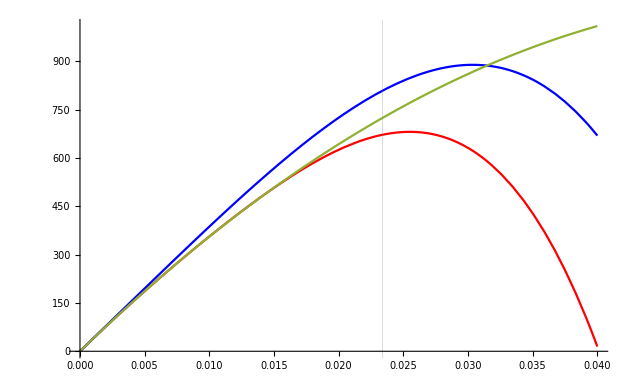

```mathematica
k = 500
t =.005* k^3/16
v= N[{T->t,K->k}]
x1 = N[1/2 Sqrt[Part[Values[v],2]/Part[Values[v],1]]]
x2 = N[(2*Part[Values[v],1])^(-1/3)]
Plot[{R10/.v,R11/.v,R9/.v},{a,0,.04},PlotStyle->{Red,Blue,Olive},GridLines->{{x1,x2},{}}]
```

```mathematica
amax3 = Solve[D[R11,a]==0,a]
```

{{a→-(-2/7)^(1/3) (1/T-(2 √2)/T)^(1/3)},{a→(2/7)^(1/3) (1/T-(2 √2)/T)^(1/3)},{a→(-1)^(2/3) (2/7)^(1/3) (1/T-(2 √2)/T)^(1/3)},{a→-(-2/7)^(1/3) (1/T+(2 √2)/T)^(1/3)},{a→(2/7)^(1/3) (1/T+(2 √2)/T)^(1/3)},{a→(-1)^(2/3) (2/7)^(1/3) (1/T+(2 √2)/T)^(1/3)}}

```mathematica
N[Values[amax3]/.v]
```

{{0.0402692-0.0697483 ⅈ},{0.0402692+0.0697483 ⅈ},{-0.0805384},{-0.0515174-0.0892308 ⅈ},{0.103035},{-0.0515174+0.0892308 ⅈ}}

```mathematica
amax3 = (2/7)^(1/3) (Together[1/T+(2 √2)/T])^(1/3)
```

(2/7 (1+2 √2))^(1/3) (1/T)^(1/3)

```mathematica
N[(2/7 (1+2 √2))^(1/3)]
```

1.03035

```mathematica
Simplify[Solve[1/2Sqrt[K/T] == b T^(-1/3) /.{T->K^3/16},b],K>0]
```

{{b→1/2^(1/3)}}

## Approximating with a 4th degree polynomial

This section is what happens if you approximate with higher order terms, but that does not work out so well because a 4th degree polynomial in a has more stationary points and asymptopically does the wrong thing.

```mathematica
amax2 =Simplify[Solve[D[R5,a]==0,a]]
```

{{a→(4 √(T/K))/(3^(1/3) (-9 T^2+√3 √(T^3 (27 T-64 (T/K)^(3/2))))^(1/3))+((-9 T^2+√3 √(T^3 (27 T-64 (T/K)^(3/2))))^(1/3))/(3^(2/3) T)},{a→(-4 3^(1/6) (3 ⅈ+√3) T √(T/K)+ⅈ 3^(1/3) (ⅈ+√3) (-9 T^2+√3 √(T^4 (27-(64 √(T/K))/K)))^(2/3))/(6 T (-9 T^2+√3 √(T^4 (27-(64 √(T/K))/K)))^(1/3))},{a→(2 ⅈ (ⅈ+√3) √(T/K))/(3^(1/3) (-9 T^2+√3 √(T^4 (27-(64 √(T/K))/K)))^(1/3))-1/(2 3^(2/3) T)(1+ⅈ √3) (-9 T^2+√3 √(T^3 (27 T-64 (T/K)^(3/2))))^(1/3)}}

0.167513-2.77556×10^-17 ⅈ

```mathematica
N[Values[amax2]//.{T->1000,K->10}]
```

{{0.167513-2.77556×10^-17 ⅈ},{-0.221432+2.77556×10^-17 ⅈ},{0.0539189+5.55112×10^-17 ⅈ}}

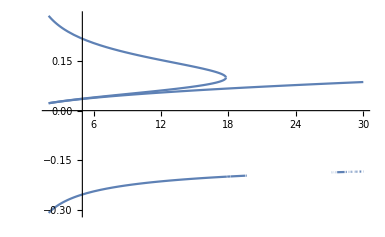

```mathematica
Plot[Append[Values[amax2],1/2Sqrt[K/T]]/.T->1000,{K,2,30}]
```